```mathematica
SetDirectory[NotebookDirectory[]];
<<RLBotIO`
<<RLBotMisc`
```

```mathematica
defaultCar
```

```mathematica
<|"time"->0,"pos"->{0,0,0},"vel"->{0,0,0},"euler"->{0,0,0},"θ"->{{1,0,0},{0,1,0},{0,0,1}},"ω"->{0,0,0},"sup"->0,"jump"->0,"dblj"->0,"grnd"->1,"boost"->0,"κ"->0.,"wheelAngle"->0.,"jumpTimer"->0.,"torque"->{0.,0.,0.},"accel"->{0.,0.,0.}|>
```

<|time→0,pos→{0,0,0},vel→{0,0,0},euler→{0,0,0},θ→{{1,0,0},{0,1,0},{0,0,1}},ω→{0,0,0},sup→0,jump→0,dblj→0,grnd→1,boost→0,κ→0.,wheelAngle→0.,jumpTimer→0.,torque→{0.,0.,0.},accel→{0.,0.,0.}|>

```mathematica
getRPY[ω0_, ωT_, J_, θ_, Δt_] := Module[{
Ω0 = Transpose[θ].ω0, 
ΩT= Transpose[θ].ωT,
T = AirTorque,
H = AirDamping,
a,b,c
},
a = Table[Δt/J T[[i]], {i, 1, 3}];
b = Table[ -Δt/J H[[i]] Ω0[[i]], {i, 1, 3}];b[[1]] = 0;
c = Table[ΩT[[i]]-(1 + Δt/J H[[i]])Ω0[[i]], {i, 1, 3}];
Table[solvePWL[a[[i]], b[[i]], c[[i]]], {i, 1, 3}]

]

ωNext[ω0_, rpy_, J_, θ_, Δt_] := Module[
{T, H, τ, ω},
T = DiagonalMatrix[AirTorque];
H = DiagonalMatrix[AirDamping * {1,(1-Abs[rpy[[2]]]), (1-Abs[rpy[[3]]])}];
τ = θ.(T.rpy+H.Transpose[θ].ω0);
ω = ω0 + τ/J Δt ;
ω *= Min[1.0, ωMaxAerial/Norm[ω]];
ω
]
```

```mathematica
drawPlots[range_] := {
which = "pos";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions[[range]]], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car[[range]]], PlotRange->All],
ImageSize->Large
],

which = "vel";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions[[range]]], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car[[range]]], PlotRange->All],
ImageSize->Large
],

which = "ω";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions[[range]]], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Norm[#[which]]& /@ predictions[[range]], PlotStyle->{Dashed, Red},PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car[[range]]], PlotRange->All],
ListLinePlot[Norm[#[which]]& /@ car[[range]], PlotStyle->Red,PlotRange->All],
PlotRange->All,
ImageSize->Large
]}
```

```mathematica
g = -651.47;
boostAccel = 1060.0;
timeLimit = 0.3;
ωMaxAerial= 5.5;
drivingSpeed = 1450;
brakingForce = 3500;
coastingForce = 525;
throttleThreshold = 0.05;
throttleForce = 1550;
maxSpeed = 2275;
minSpeed = 10;


carMass = 180.0;
carInertiaMoment =10.5;
dodgeLimit = 1.25;
jumpMax = 0.2;
jumpImpulse = 52500;
jumpForce = 262500;
liftoffTime = 0.045;
throttleForce = 12000;
boostForce = 178500;
AirTorque = {-400.0, -130.0, 95.0};
AirDamping  = {-50.0, -30.0, -20.0};

κ[x_]:= Interpolation[({{0, 0.0069}, {500, 0.00398}, {1000, 0.00235}, {1500, 0.001375}, {1750, 0.0011}, {2300, 0.00088}}), InterpolationOrder->1][x]





AirDodge[state_, input_, Δt_] := Module[{
next = state

},
(* TODO *)
next
]

drivingForceForward[state_, input_] := Module[{
boost=input["boost"],
steering=input["steer"],
throttle=input["thr"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"],
turnDamping
},
turnDamping = (-0.07186693033945346 Abs[steering]-0.055453237281917644  Abs[ωu]+0.0006255296371672214 Abs[vl]) vf;
If[boost == 1,

(* boosting *)
If[vf < 0,
brakingForce,
If[0 <vf <drivingSpeed,
(maxSpeed - Abs[vf]),
If[vf > maxSpeed,
98.25785130764065 Abs[ωu],
boostAccel +turnDamping
]
]
],

(* not boosting *)
If[throttle * Sign[vf] > -0.001 && Abs[vf] > minSpeed, 
If[Abs[throttle] <  throttleThreshold && Abs[vf] > minSpeed,
-coastingForce Sign[vf] + turnDamping,
If[Abs[vf]>drivingSpeed,
turnDamping,
throttle(1550 - Abs[vf]) + turnDamping
]
],
brakingForce Sign[throttle]
]
]
]

drivingForceLeft[state_, input_] := Module[{
boost=input["boost"],
steering=input["steer"],
throttle=input["thr"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"]
},
 (1380.4531378064655 steering+7.82811881088291 throttle-15.006402973550104 vl+668.1208332047357 ωu)(1-Exp[-0.0011607974131331873 Abs[vf]])
]

drivingTorqueUp[state_, input_] := Module[{
steering=input["steer"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"]
},
15(steering κ[Abs[vf]]vf- ωu)
]

AirDodge[state_, input_, Δt_] := Module[{},
state
]

Jump[state_, input_, Δt_] := Module[{
next=state,
θ=state["θ"],
a = 0,
forward, left, up
},
{forward, left, up} = Transpose[θ];
If[state["jump"] == 0, 
next["jump"] = 1;
next["jumpTimer"] = 0;
,
If[state["grnd"] == 1,
a += g up;
];
If[state["jumpTimer"] == 0,
a+=1/Δt jumpImpulse/carMass up;
];
If[state["jumpTimer"] < jumpMax,
a+=jumpForce/carMass up;
];
If[state["jumpTimer"] > liftoffTime,
next["grnd"] = 0
];
next["jumpTimer"]+=Δt;
next["accel"]+=a;
next["vel"]+=a Δt;
next["pos"]+=a Δt^2;
];
next
]

GroundControl[state_, input_, Δt_] := Module[{
next = state,
forward=(state["θ"][[All, 1]]),
left=(state["θ"][[All, 2]]),
up=(state["θ"][[All, 3]]),
Fforward,Fleft,Tup
},
Fforward=drivingForceForward[state, input];
Fleft=drivingForceLeft[state, input];
Tup=drivingTorqueUp[state, input];
next["vel"]=state["vel"] + {1,1,0}*(Fforward*forward + Fleft*left) Δt;
next["pos"]=state["pos"] + next["vel"]Δt;
next["ω"]= {0.9, 0.9, 1.0}*state["ω"] + Tup*up Δt;
next["θ"]=RotationMatrix[next["ω"].up Δt, up].state["θ"];
next
]

AerialControl[state_, input_, Δt_] := Module[{
next = state,
θ = state["θ"],
rpy = {input["roll"], input["pitch"], input["yaw"]},
ωAvg, ωLocal, T, H, 
forward, left, up
},
{forward, left, up} = Transpose[θ];
next["time"] += Δt;
next["accel"] = {0, 0, g};
next["accel"]+=forward/carMass(input["boost"](boostForce + throttleForce));
next["accel"]+=forward/carMass((1 - input["boost"]) input["thr"] throttleForce);
next["vel"]=state["vel"] + next["accel"] Δt;
next["pos"]=state["pos"] + next["vel"] Δt; 
T = DiagonalMatrix[AirTorque];
H = DiagonalMatrix[AirDamping * {1,(1-Abs[rpy[[2]]]), (1-Abs[rpy[[3]]])}];
next["torque"] = θ.(T.rpy+ H.Transpose[θ].state["ω"]);
next["ω"] = state["ω"] + next["torque"]/carInertiaMoment Δt ;
ωAvg = 1/2(state["ω"] +next["ω"]);
next["θ"] = RotationMatrix[Norm[ωAvg]Δt,Normalize[ωAvg]].θ;
next["ω"] *= Min[1.0, ωMaxAerial/Norm[next["ω"]]];
next["vel"] *= Min[1.0, maxSpeed/Norm[next["vel"]]];
next
]

CarControl[state_, input_, Δt_] := Module[{next},
next = If[state["grnd"] == 0,
AerialControl[state, input, Δt],
GroundControl[state, input, Δt]
];
If[input["jump"] == 1,
next = If[state["dblj"] == 0,
Jump[next, input, Δt],
AirDodge[next, input, Δt]
];
];
next
]
```

```mathematica
simulate[substeps_, delay_, car_, inputs_] := Module[{
predictions,lastPrediction,Δt
},
predictions = Table[car[[i]], {i, 1, delay}];
lastPrediction = predictions[[-1]];
Do[
Δt = car[[delay + i + 1]]["time"] - car[[delay + i]]["time"];
Do[
lastPrediction = CarControl[lastPrediction, inputs[[i]],  Δt/substeps],
{j, 1, substeps}
];
AppendTo[predictions,lastPrediction];
,
{i, 1, Length[car]-delay-1}
];
predictions
]
```

```mathematica
rawcar[[1]]
```

<|time→1.69105,pos→{0.,-4608.,16.9413},vel→{0.,0.011285,9.7853},euler→{-101,16384,0},θ→{{6.12295×10^-17,-1.,5.92919×10^-19},{0.999953,6.12323×10^-17,0.0096831},{-0.0096831,0.,0.999953}},ω→{0.001774,0.,0.},sup→0,jump→0,dblj→0,grnd→1,boost→100,κ→0.,wheelAngle→0.,jumpTimer→0.,torque→{0.,0.,0.},accel→{0.,0.,0.}|>

```mathematica
{rawcar, rawinputs} = ImportEpisode[NotebookDirectory[] <> "data.txt"]
```

{{<|time→95.5311,pos→{959.37,-2789.08,17.01},vel→{0.,0.,8.31},euler→{-100,16680,0},θ→RLBotIO`Private`EulerAnglesToMatrix[{-0.00958738,1.59917,0.}],ω→{0.0002,0.,0.},sup→0,jump→0,dblj→0,grnd→1,boost→100,κ→0.,wheelAngle→0.,jumpTimer→0.,torque→{0.,0.,0.},accel→{0.,0.,0.}|>,<|time→95.5311,14,accel→{1}|>,1552,<|time→110.278,pos→{768.49,3967.59,17.01},vel→{0.,0.,8.31},euler→{-100,16680,0},8,wheelAngle→0.,jumpTimer→0.,torque→{0.,0.,0.},accel→{0.,0.,0.}|>},1}
 |  |  |  |

```mathematica
(* wheel order: FL, FR, BL, BR *)
brakeTorque = 10500;
driveTorque = 288000;
stopThreshold = 25;
idleBrakeFactor = 0.15;
wheelSteerFactor = {1, 1, 0, 0};
wheelRadii = {12, 12, 15, 15};
XY = DiagonalMatrix[{1,1,0}];
wheelOffsets = ({{51.25, -25.9, -6.0}, {51.25, 25.9, -6.0}, {-33.75, -29.5, -4.3}, {-33.75, 29.5, -4.3}});
axleSeparation = wheelOffsets[[1,1]] - wheelOffsets[[3,1]];
axleWidth = wheelOffsets[[2,2]] - wheelOffsets[[2, 1]];
driveTorqueScale[v_] := Interpolation[({{0, 1.0}, {1400, 0.1}, {1410, 0.0}, {3000, 0.0}}), InterpolationOrder->1][v]
steeringAngle[v_] := Interpolation[({{0, 0.5222688347082791}, {500, 0.3144856419291022}, {1000, 0.18027854909699828}, {1500, 0.10506707564080665}, {1750, 0.08465545003873295}, {3000, 0.034471998056140006}}), InterpolationOrder->1][v]
LongCurve[R_] := 0.0 (* ? *)
LatCurve[R_] :=  Interpolation[({{0, 1.0}, {1.0, 0.2}}), InterpolationOrder->1][R]
handbrakeLongCurve[R_] :=  Interpolation[({{0, 0.5}, {1.0, 0.9}}), InterpolationOrder->1][R]
handbrakeLatCurve[R_] :=  0.1 (* ? *)
wallFriction[nz_] := Interpolation[({{0, 0.1}, {0.707, 0.5}, {1.0, 1.0}}), InterpolationOrder->1][nz]
```

Null^2

Null^2

```mathematica
GroundControl[state_, input_, Δt_] := Module[{
next = state,
θ = state["θ"],
vCarLocal = state["vel"].state["θ"],
ωCarLocal = state["ω"].state["θ"],
carForward=(state["θ"][[All, 1]]),
carLeft=(state["θ"][[All, 2]]),
carUp=(state["θ"][[All, 3]]),
throttle = input["thr"],
wheelAngle = state["wheelAngle"],
FLocal = {0, 0, 0}, 
τLocal = {0, 0, 0},
wheelForward, wheelLeft,wheelSupport,
ϕWheel,vWheel,FWheel,
vLong,vLat,R, μLong, μLat, W
},
W  = wallFriction[carUp[[3]]];
Do[
vWheel=vCarLocal+Cross[ωCarLocal,wheelOffsets[[w]]];
{wheelForward, wheelLeft} = RotationMatrix[wheelSteerFactor[[w]]*wheelAngle,{0, 0, 1}][[1;;2]];
vLong = vWheel.wheelForward;
vLat = vWheel.wheelLeft;
R = Abs[vLat]/(Abs[vLong] + Abs[vLat]);
μLong = If[input["brake"] == 1, handbrakeLongCurve[R], LongCurve[R]];
μLat = If[input["brake"] == 1, handbrakeLatCurve[R], LatCurve[R]];
wheelSupport = 1/2 Abs[wheelOffsets[[w, 1]]]/axleSeparation;
(* frictional forces *)
FWheel = -W{μLong  vLong, μLat  vLat, 0.0};

(* throttle/boost/brake forces *)
If[Abs[throttle] < 0.01 && Abs[vLong] > stopThreshold,
(* coasting *)
FWheel[[1]] +=-9.0brakeTorque  Sign[vLong];
,
FWheel[[1]] += input["thr"]driveTorque driveTorqueScale[Abs[vLong]]
];

FLocal += wheelSupport * FWheel;
τLocal += 0.0000001Cross[XY.wheelOffsets[[w]], FWheel];
,
{w, 1, 4}
];
next["wheelAngle"] = steeringAngle[Abs[vCarLocal[[1]]]];
next["vel"]=state["vel"] + (θ.FLocal)/carMass Δt;
next["pos"]=state["pos"] + next["vel"]Δt;
next["ω"]= {0.9, 0.9, 1.0}*state["ω"] + (θ.τLocal)/carInertiaMoment Δt;
next["θ"]=RotationMatrix[Norm[next["ω"]] Δt, Normalize[next["ω"]]].state["θ"];
next
]
```

```mathematica
which =300;
Δt = car[[which+1]]["time"] - car[[which]]["time"];
p = CarControl[car[[which]], inputs[[which]], Δt];
p["vel"] - car[[which+1]]["vel"]
```

{-0.000827057,-0.0000525878,-0.0671811}

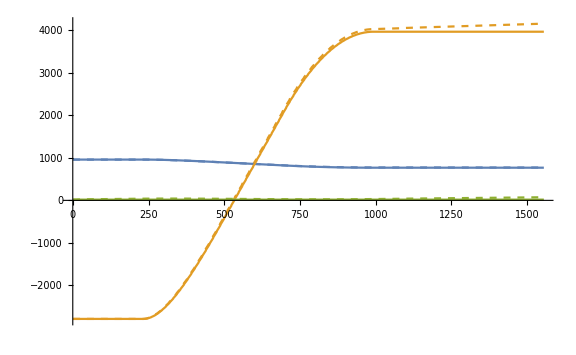
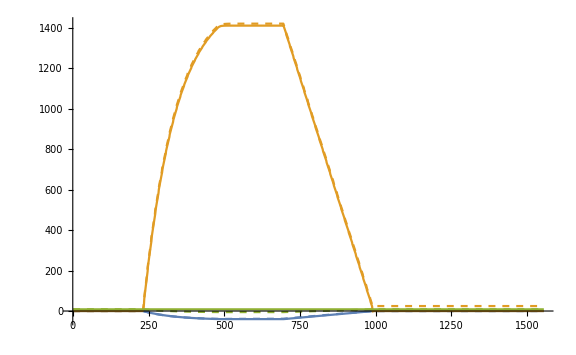
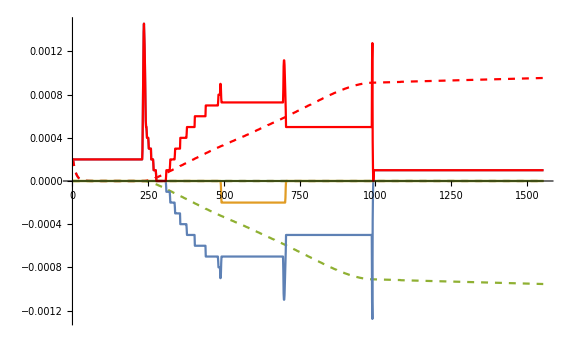

```mathematica
delay = 2;
substeps = 1;
predictions = simulate[substeps, delay, car[[1;;-1]], inputs[[1;;-1]]];
drawPlots[1;;-1]
```